3.87831×10^7

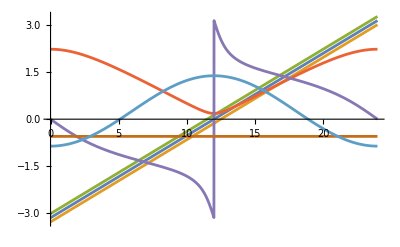

```mathematica
SOLAR=1367;
DiasJulianos=List[17,47,75,105,135,162,198,228,258,288,318,344];
latitud=-31.4°; (* ϕ *)
inclinacion=latitud; (* β *)
acimut=Pi; (* γ *)
n=17;
anguloSolar=(h-12)Pi/12;  (* ω *)
declinacion=(23.45*Pi/180)*Sin[2*Pi*(284+n)/365]; (* δ *)
cenit=ArcCos[ Cos[latitud]Cos[declinacion]Cos[anguloSolar]+Sin[latitud]Sin[declinacion]];
acimutSolar=If[anguloSolar<0,-1,1]Abs[ArcCos[(Cos[cenit]Sin[latitud]-Sin[declinacion])/(Sin[cenit]Cos[latitud])]];
incidencia=ArcCos[Cos[cenit]Cos[inclinacion]+Sin[cenit]Sin[inclinacion]Cos[acimutSolar-acimut]];
excentricidad = 1+0.033Cos[2Pi*n/365];
anguloSalida=ArcCos(-Tan(declinacion)Tan(latitud));
HoJ=(24*3600/Pi)*SOLAR*excentricidad(Cos[latitud]*Cos[declinacion]*Sin[anguloSalida]+anguloSalida Sin[latitud]Sin[decl]);
Ho=HoJ/3600000;
angulo1=anguloSolar-Pi/24;
angulo2=anguloSolar+Pi/24;
IoJ=(12*3600/Pi)*SOLAR*excentricidad(Cos[latitud]Cos[declinacion](Sin[angulo2]-Sin[angulo1])+(angulo2-angulo1)Sin[latitud]Sin[declinacion]);
Io=IoJ/3600000;
Rb=Cos[incidencia]/Cos[cenit];
Plot[{anguloSolar, angulo1, angulo2,cenit,acimutSolar, inclinacion, Io},{h, 0, 24}]
```